Autor: Radosław Terelak

# Metody numeryczne

## (kierunek Informatyka)

## Projekt 2

Metoda Newtona

Napisać procedurę realizującą algorytm metody stycznych (Newtona) (argumenty:  f, x_0,  e).
Napisać także procedurę realizującą algorytm metody Newtona dla układu dwóch równań nieliniowych (argumenty:  f, g, v_0,  e).

Korzystając z napisanych procedur:

a) Wyznaczyć pierwiastek 6 stopnia ze 101 z dokładnością 10^-10.

b) W pewnym układzie elektrycznym z diodą tunelową natężenie prądu i oraz napięcie u spełniają układ równań:

i=k u (u^2/3-3/2 u+2),
u/r+i=j,

gdzie k=1 mA/V^3, j=1 mA, r= 10 kΩ. Wykorzystując metodę Newtona wyznaczyć natężenie prądu oraz napięcie. Rozwiązanie zilustrować graficznie (można do tego celu wykorzystać instrukcję ContourPlot).

## Rozwiązanie

### Program (jedno równanie)

```mathematica
newton1[f_,x0_,e_] := Module[{xs,xn},
xs = x0+2e;
xn = x0;
While[Abs[xn-xs]>e,
xs = xn;
xn = xs - f[xs]/f'[xs];
];
Return[xn]
]
```

### Przykład testowy (jedno równanie)

```mathematica
Clear[f];
f[x_]:=x^2-3; (* przykład z wykładu *)

newton1[f,3., 0.1]
```

1.73214

### Program (układ dwóch równań)

```mathematica
(* Funkcja wsk3 z pliku Wskazówka na platformie *)
wsk3[f_,g_,a_,b_]:=Module[{c,j,c1},
(* Symboliczne wyznaczenie macierzy Jacobiego *)
j= {{D[f[x,y],x],D[f[x,y],y]}, {D[g[x,y],x], D[g[x,y],y]}};
(* macierz Jacobiego w punkcie (a,b) *)
c=j/.{x->a, y->b};
(* macierz odwrotna *)
c1 = Inverse[c];
Return[c1]]

newton2[f1_,f2_,x0_,e_] := Module[{j,xs,xn,p},
xs=x0+2e;
xn=x0;
While[Norm[xn-xs]>e,
xs=xn;
p=wsk3[f1,f2,xs⟦1⟧,xs⟦2⟧];
xn=xs-p.{f1[xs⟦1⟧,xs⟦2⟧],f2[xs⟦1⟧,xs⟦2⟧]};
];
Return[xn]
]
```

### Przykład testowy (układ dwóch równań)

```mathematica
(* Dane z wykładów *)
```

```mathematica
t1[x_,y_]:=x^2+y^6;
t2[x_,y_]:=2*x*y+3x^2;
wsk3[t1,t2,1,1]
```

{{-1/22,3/22},{2/11,-1/22}}

```mathematica
t1[x_,y_]:=x^2+y^2;
t2[x_,y_]:=x+2*x*y;
newton2[t1,t2,{1,1},0.1]
```

{0,1/16}

### Zadanie a)

```mathematica
g[x_]=x^6-101;
NumberForm[newton1[g,150.,10^-10], 11]
```

2.158010544

### Zadanie b)

```mathematica
Clear[k,j,r,f1,f2];
```

{2.38767,0.761233}

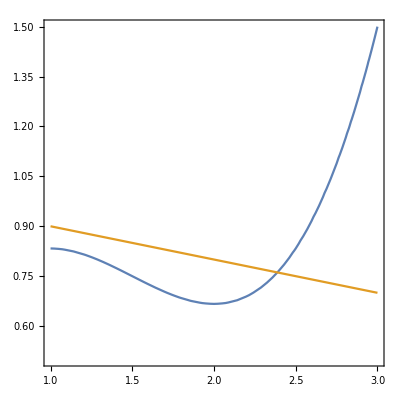

```mathematica
k=1; (* mA/V^3*)
j=1; (* mA *)
r=10; (* 10 kΩ*)
(* Układ równań *)
f1[u_,i_]:=k*u*(u^2/3-3/2*u+2)-i;  
f2[u_,i_]:=u/r+i-j; 
N[newton2[f1, f2,{3,3},10^-10]]
ContourPlot[{f1[x,y], f2[x,y]},{x,1,3},{y,0.5,1.5}]
```